```mathematica
Copyright © 2021 Franz Utermohlen. All rights reserved.
```

## Spin-wave Hamiltonian

```mathematica
Clear["Global`*"];
a=1;
(*Coordination number*)
q=4;
(*Vectors*)
a1=a{1,0,0};
a2=a{0,1,0};
a3=a{0,0,1};
b1=2π Cross[a2,a3]/(a1.Cross[a2,a3]);
b2=2π Cross[a3,a1]/(a2.Cross[a3,a1]);
b3=2π Cross[a1,a2]/(a3.Cross[a1,a2]);
Γpoint={0,0,0};
Mpoint=(π/(2a)){1,1,0};
Xpoint=(π/a){1,0,0};
(*Mpoint=(b1+b2)/2;
Xpoint=b1;*)
δ1=a1;
δ2=a2;
(*Ignore the z-components of all of the vectors, since they are zero*)
{a1,a2,b1,b2,Γpoint,Xpoint,Mpoint,δ1,δ2}=Most/@{a1,a2,b1,b2,Γpoint,Xpoint,Mpoint,δ1,δ2};
(*Scalars*)
γk[kvec_]:=1/q(Exp[I kvec.δ1]+Exp[I kvec.δ2]+Exp[-I kvec.δ1]+Exp[-I kvec.δ2]);
η2=({{1, 0}, {0, -1}});
(*η4=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});*)
(*η8=DiagonalMatrix[{1,1,1,1,-1,-1,-1,-1}];*)
(*Spin-wave Hamiltonian*)
h[kvec_]:=η2.({{1, γk[kvec]}, {Conjugate[γk[kvec]], 1}});
(*h[kvec_]:=η4.({{1, 0, 0, γk[kvec]}, {0, 1, γk[kvec], 0}, {0, Conjugate[γk[kvec]], 1, 0}, {Conjugate[γk[kvec]], 0, 0, 1}});*)
(*h[kvec_]:=η4.({{1, 0, 0, Conjugate[γk[kvec]]}, {0, 1, Conjugate[γk[-kvec]], 0}, {0, γk[-kvec], 1, 0}, {γk[kvec], 0, 0, 1}});*)

(*Number of magnon modes in the spectrum*)
numModes=Length[
Select[
Chop[
Re[
N[
Eigenvalues[
h[{N[Sqrt[E]],N[Sqrt[EulerGamma]]}]
]
]
]
]
,#≥0&]
];

(*Eigenvalues*)
eigenvals[kvec_]:=
Sort[
Chop[
Re[
N[
Eigenvalues[
h[kvec]
]
]
]
]
,Greater][[1;;numModes]];
```

## Magnon band structure

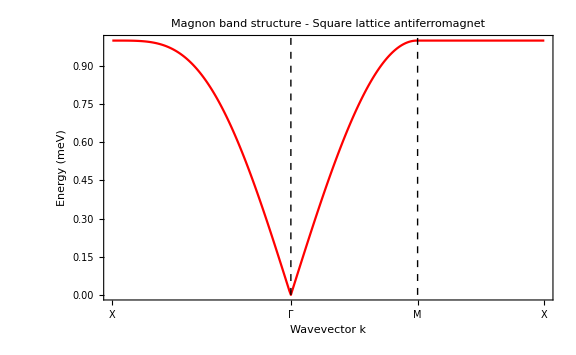

```mathematica
(*======================================= INPUT =======================================*)

(*================== k-space path ==================*)
(*K–Γ–M–K*)
path={"X","Γ","M","X"};

(*Γ–M–K–Γ*)
(*path={"Γ","M","X","Γ"};*)

(*Γ–K–M–K–Γ*)
(*path={"Γ","X","M","X","Γ"};*)
(*===================================================*)

(*=====================================================================================*)

(*Number of steps*)
numSteps=300;
(*numSteps=500;*)
(*Number of high symmetry points*)
numHighSymmetryPoints=Length[path];
(*Number of legs in the path;
Note: a leg is the part of the path from one high symmetry point point to the next; for example, the path K–Γ–M–K has 3 legs, namely K–Γ, Γ–M, and M–K*)
numLegs=numHighSymmetryPoints-1;
(*k-vector coordinate for each high symmetry point*)
point=Table[
If[path[[i]]=="Γ",
Γpoint
,(*else*)
If[path[[i]]=="X",
Xpoint
,(*else*)
If[path[[i]]=="M",
Mpoint
]
]
]
,{i,1,numHighSymmetryPoints}];
(*List containing the displacement vector for each leg*)
displacementVectors=Table[point[[i+1]]-point[[i]],{i,1,numLegs}];
(*List containing directional (i.e., unit) vector for each displacement vector*)
directionalVectors=Normalize/@displacementVectors;
(*List containing the distance corresponding to each displacement vector (i.e., the length of each leg)*)
distances=Norm/@displacementVectors;
(*Total distance in k-space covered in our path*)
totDist=Total[distances];
(*Step distance in k-space*)
stepDist=totDist/(numSteps-1);
(*List containing the number of steps corresponding to each leg*)
numStepsList=Table[Round[numSteps(distances[[i]]/totDist)],{i,1,numLegs}];
(*Check that they add to numSteps*)
(*Print[Total[numStepsList]==numSteps];*)
(*Lists containing the numbers corresponding to the first and last step of each leg*)
lastStep=Table[Total[numStepsList[[1;;i]]],{i,1,numLegs}];
firstStep=Join[{1},(lastStep[[1;;numLegs-1]]+1)];
(*Initialize the list containing the k vector for each step*)
kvecs=ConstantArray[0,numSteps+1];
(*Loop over all of the steps*)
stepIndex=0;
Do[
Do[
stepIndex+=1;

If[stepIndex==firstStep[[leg]],
kvecs[[stepIndex]]=point[[leg]];
,
kvecs[[stepIndex]]=kvecs[[stepIndex-1]]+stepDist directionalVectors[[leg]];
];

,{step,firstStep[[leg]],lastStep[[leg]]}];
,{leg,1,numLegs}];

(*Put in the last k point in by hand (corresponding to the last high symmetry point)*)
kvecs[[numSteps+1]]=point[[numHighSymmetryPoints]];

(*Check to see how far off we are at each of the high symmetry points*)
(*Do[
Print[
ToString[
N[Norm[kvecs[[firstStep[[i]]-1]]-point[[i]]]/stepDist]
]
<>
" steps"
];
,{i,2,numHighSymmetryPoints-1}]*)

(*===Plot the magnon band structure===*)
data=Table[eigenvals[kvecs[[step]]] ,{step,1,numSteps+1}];

(*If[Dimensions[data]≠{numSteps+1,2},Print["Error: Unphysical magnon band structure: the magnon spectrum is gapless ==> 2D system is not ferromagnetically stable."]
,(*else*)*)

Emin=Min[data];
Emax=Max[data];
ΔE=Emax-Emin;
(*Maximum energy to plot on the y-axis*)
ymin=0;
(*ymin=Automatic;*)
ymax=Automatic;

lineStyle={Black,Dashed};
yminLine=0;
ymaxLine=1.5Emax;
highSymmetryPointsVerticalLines=Table[Line[{{firstStep[[i]],yminLine},{firstStep[[i]],ymaxLine}}],{i,2,numHighSymmetryPoints-1}];
ticks={{Automatic,Automatic},{Join[Table[{firstStep[[i]],path[[i]]},{i,1,numHighSymmetryPoints-1}],{{lastStep[[numHighSymmetryPoints-1]]+1,path[[numHighSymmetryPoints]]}}],None}};

(*Make plot*)
ListLinePlot[Transpose[data],
PlotRange->{{1,numSteps+1},{ymin,ymax}},
Frame->True,
(*Frame->{{True,False},{True,False}},*)
FrameLabel->{{"Energy (meV)",None},{"Wavevector k",None}},
FrameTicks->ticks,
PlotLabel->"Magnon band structure - Square lattice antiferromagnet",
(*PlotLegends->SwatchLegend[{"E_+","E_-"}],*)
PlotStyle->Red,
LabelStyle->Directive[16,Black],
FrameStyle->Directive[18,Black],
Epilog->{Directive[lineStyle],highSymmetryPointsVerticalLines},
ImageSize->Large]
```

## Path in k-space

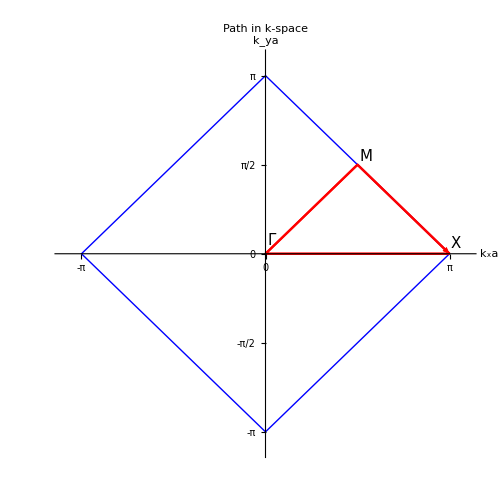

```mathematica
(*Rotation matrix*)
R[θ_]:=({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}});
(*Number of corners in the 1st Brillouin zone*)
numCorners=4;
(*A corner of the 1st Brillouin zone*)
corner=Xpoint;
(*Corners of 1st Brillouin zone*)
brillouinZoneEdges=Table[R[2π i/numCorners].corner,{i,1,numCorners+1}];
(*x- and y-components of vectors that make up the brillouinZoneEdges*)
brillouinZoneEdgesx=brillouinZoneEdges[[All,1]];
brillouinZoneEdgesy=brillouinZoneEdges[[All,2]];
(*x and y components of infinitesimal vectors that make up the k-space path*)
kvecsx=kvecs[[1;;numSteps+1,1]];
kvecsy=kvecs[[1;;numSteps+1,2]];
(*Minimum and maximum kx and ky values to plot*)
xmin=Min[Flatten[{brillouinZoneEdgesx,kvecsx}]];
xmax=Max[Flatten[{brillouinZoneEdgesx,kvecsx}]];
xcushion=(xmax-xmin)/20;
ymin=Min[Flatten[{brillouinZoneEdgesy,kvecsy}]];
ymax=Max[Flatten[{brillouinZoneEdgesy,kvecsy}]];
ycushion=(ymax-ymin)/20;
(*Tick marks*)
xticks=Table[Round[i,π/2],{i,xmin-π,xmax+π,π/2}];
yticks=Table[Round[i,π/2],{i,ymin-π,ymax+π,π/2}];
ticks={xticks,yticks};
(*ticks=None;*)
brillouinZoneColor=Blue;
pathColor=Red;
plotsize=500;
plotsettings={PlotRange->{{xmin-xcushion,xmax+xcushion},{ymin-ycushion,ymax+ycushion}},PlotLabel->"Path in k-space",AxesLabel->{"k_xa","k_ya"},LabelStyle->Directive[16,Black],FrameStyle->Directive[14,Black],Ticks->ticks,AspectRatio->Automatic,PlotStyle->Directive[14,pathColor],ImageSize->plotsize};

(*Sketch the 1st Brillouin zone and the path in k-space*)
highSymmetryPointLabels=Epilog->{
{Text[Style["Γ",15],(Γpoint+xcushion/3{1,0}+0.75ycushion{0,1})]}
,
{Text[Style["X",15],(Xpoint+xcushion/3{1,0}+0.6ycushion{0,1})]}
,
{Text[Style["M",15],(Mpoint+1.4xcushion ycushion{1,1})]}
};
pathPlot=ListLinePlot[Transpose[{kvecsx,kvecsy}],Evaluate[plotsettings,highSymmetryPointLabels]]/.Line->Arrow;
brillouinZonePlot=Graphics[{brillouinZoneColor,Line[brillouinZoneEdges]}];

Show[pathPlot,brillouinZonePlot,pathPlot]
```